```mathematica
ClearAll["Global`*"]; (* This function clears any past definitions of the variables *)



(* THERMOPHYSICAL PROPERTIES OF THE PARAFFIN *)

Tm=303; (* melting temprerature of the paraffin *)
ρs=880;ρl=760;ρ=ρl; (* density at solid and liquid states *)
ks=0.24;kl=0.15; (* thermal conductivity at solid and liquid states *)
cps=2.4*10^3;cpl=1.8*10^3; (* specific heat at solid and liquid states *)
q=179*10^3; (* latent heat of fusion*)
vd=3.42;vk=vd/ρ; (* dynamic viscosity (vd) and kinematic viscosity (vk) of paraffin *)


(* FORMULAS AND TRANSFORMATIONS*)

αs=ks/(ρs cps);αl=kl/(ρl cpl); (* thermal diffusivity at solid and liquid states *)
pr=vk/αl; (* Prandtl number*)
gdot=(G kl(T0-Tm))/r^2; (* heat sink parameter *)
ξ=gdot/(ρ q)((r^2 τ)/αl); (* mass proportion of liquid in the mixture; t taken as (r^2 τ)/αl *)
T0=Tm+(q ste)/cpl;(* temperature outside the sphere; it depends on the stefan number desired for the simulation*)

γ=ks/kl;
Γ=αs/αl;
θi=(Ti-Tm)/(T0-Tm); (* dimensionless initial temperature *)



keq=1;  (* equivalent thermal conductivity *)

(* since Rayleigh number = 0 (i.e. ≤ 5×10^4) for figure 3(c), keq is assumed equal to 1 *) 


(* PARAMETER VALUES *)

r=0.05; (* radius of the sphere *)
Ti=295; (* initial temperature of the paraffin *)


(* PARAMETER VALUES SPECIFIC TO FIGURE 3(c) OF BECHIRI ET AL. 2020 *)

ste=0.05; (* Stefan number *)
ra=0; (* Rayleigh number *)
bi=10; (* Biot number *)
G=0; (* dimensionless heat sink parameter *)
```

```mathematica
(* SOLVING THE EQUATION SYSTEM (6) *)
```

```mathematica
lhs=((keq bi)/splus[τ] Exp[-splus[τ]^2/(4keq τ)])/(keq Exp[-1/(4 keq τ)]-bi(Exp[-1/(4 keq τ)]-1/splus[τ] Exp[-splus[τ]^2/(4keq τ)]-√(π/(4keq τ))(Erfc[1/(2 √(keq τ))]-Erfc[splus[τ]/(2 √(keq τ))])))+G/(6splus[τ])((bi(splus[τ]^2-1)-2keq)/(bi+splus[τ](keq-bi)))-2/splus[τ]∑_(n=1)^∞ (γ θi+(G splus[τ]^2)/(n^2 π^2))Exp[-(n^2 π^2 Γ τ)/splus[τ]^2]
```

(2.5743 (-1.+EllipticTheta[3,0.,2.71828^(-(10.2285 τ)/splus[τ]^2)]))/splus[τ]+(10 ⅇ^(-splus[τ]^2/(4 τ)))/((ⅇ^(-1/4/τ)-10 (ⅇ^(-1/4/τ)-1/2 √π √(1/τ) (Erfc[1/(2 √τ)]-Erfc[splus[τ]/(2 √τ)])-(ⅇ^(-splus[τ]^2/(4 τ)))/splus[τ])) splus[τ])

```mathematica
rhs=((1-ξ)/ste)splus'[τ]
```

20. splus'[τ]

```mathematica
sol=NDSolve[{lhs== rhs,splus[0.001]==1},splus[τ],{τ,0.01,4}] (* this line gives solution of equation system (6) with initial condition S^+(0.001)=1; the solution is stored in the variable 'sol'*)
```

NDSolve::ndsz: At τ == 0.141861, step size is effectively zero; singularity or stiff system suspected.

{{splus[τ]→InterpolatingFunction[{{0.01, 0.141861}}, <>][τ]}}

InterpolatingFunction::dmval: Input value {0.00100286} lies outside the range of data in the interpolating function. Extrapolation will be used.

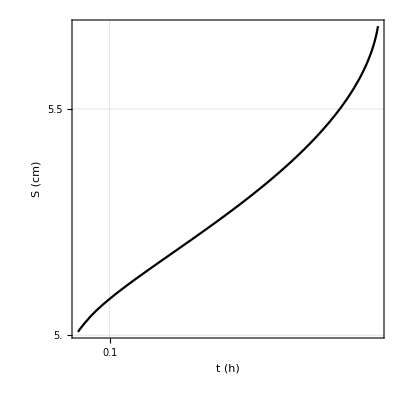

```mathematica
Plot[Evaluate[splus[τ]/.sol],{τ,0.001,0.141},
PlotTheme->{"Detailed","Monochrome"},AspectRatio->1, 
PlotLegends->None,FrameLabel-> {Style["t (h)",15],Style["S (cm)",15]},
FrameTicks->{Table[{0.0158(* τ = 0.158 <=> t = 1 h *)i,0.1i},{i,1,200}],
Table[{1+0.02 i,r*100*(1+0.02 i)},{i,0,200}]}] (* plotting the solution of the differential equation *)
```

```mathematica
(* 

NOTES:

  - since Rayleigh number = 0 (i.e. Ra ≤ 5×10^4), keq is assumed equal to 1

  - the equation is solved with initial condition S^+(0.001)=1, i.e. the initial condition is set at τ=0.001. 
This is done because having τ=0 leads to the indeterminate form 1/0 appearing inside equation 6.1.  

- τ = 0.158 units corresponds to t = 1h, τ = 0.316 units corresponds to t = 2h, and so on. τ = 3.78947 units corresponds to t = 24 h.

*)
```